## Huntington‒Hill Apportionment

Huntington‒Hill Method of Apportionment.
h is house size, p is a list of populations, g is a list of guaranteed seats.

```mathematica
HHRoundingFn=Function[x,Sqrt[(x-1)x]];
```

```mathematica
HHLowDivs=Function[{p,g,a},
Table[If[a[[i]]<g[[i]],∞,If[HHRoundingFn[a[[i]]+1]==0,∞,p[[i]]/HHRoundingFn[a[[i]]+1]]],
{i,1,Length[p]}
]
];
HHHighDivs=Function[{p,g,a},
Table[
If[a[[i]]<=g[[i]],∞,If[HHRoundingFn[a[[i]]]==0,∞,p[[i]]/HHRoundingFn[a[[i]]]]],
{i,1,Length[p]}
]
];
```

```mathematica
HHFoundCond=Function[{p,g,a},Max[HHLowDivs[p,g,a]]<=Min[HHHighDivs[p,g,a]]];
```

```mathematica
HHAddSet=Function[{p,g,a},Ordering[HHLowDivs[p,g,a],-1,NumericalOrder]];
HHDelSet=Function[{p,g,a},Ordering[HHHighDivs[p,g,a],1,NumericalOrder]];
```

```mathematica
DivisorMethodAllocation=Function[{d,p,g},
Module[{quota,geom},
quota:=g+p/d;
geom:=HHRoundingFn[Floor[#]+1]&/@quota;
MapThread[{m,q}|->Floor[q]+Boole[q>m],{geom,quota}]
]
];
```

```mathematica
HuntingtonHillApportionment=Function[{names,h,p,g},
MapThread[{#1,#2}&,
{names,
NestWhile[
x|->Module[{a,asum,nexta,priority,i,i2,k},
{a,asum,priority}=x;
i=Ordering[priority,-1,NumericalOrder][[1]];
i2=Ordering[priority,-2,NumericalOrder][[1]];
k:=p[[i]]/priority[[i2]];
(* We want to find the minimal x∈Integers s.t. p[[i]]/HHRoundingFn[x+1] <= priority[[i2]] && 0 <= x. After 0 this polynomial is increasin; thus it suffices to find x^2 + x == k and take the Floor[x+1] (effectively the ceiling, but going up when the priority is matched by another position).
*)
nexta=Min[Floor[-1/2+1/2 √(4 k^2+1)+1],h-asum+a[[i]]];
asum=asum+nexta-a[[i]];
a[[i]]=nexta;
priority[[i]]=If[HHRoundingFn[a[[i]]]==0,∞,p[[i]]/HHRoundingFn[a[[i]]+1]];
{a,asum,priority}
],
{g,Total[g],HHLowDivs[p,g,g]},
x|->x[[2]]<h
][[1]]
}
]
];
```

## House Size, Electors, and Voter Power

### The Current House and Electors

#### Census Data

USA state populations from the 2020 census.
https://www.census.gov/data/tables/time-series/demo/popest/2020s-state-total.html

```mathematica
usaPopulationDataCSV=FileNameJoin[{NotebookDirectory[],"NST-EST2022-ALLDATA.csv"}];
usaPopulationData=Import[usaPopulationDataCSV,"Dataset",HeaderLines->1];
```

```mathematica
usaVotersDataCSV=FileNameJoin[{NotebookDirectory[],"2022-voters.csv"}];
usaVotersCSVData=Import[usaVotersDataCSV,"Dataset",HeaderLines->1];
```

Select out the states that actually get house seats.

```mathematica
usa50States={"Alabama","Alaska","Arizona","Arkansas","California","Colorado","Connecticut","Delaware","Florida","Georgia","Hawaii","Idaho","Illinois","Indiana","Iowa","Kansas","Kentucky","Louisiana","Maine","Maryland","Massachusetts","Michigan","Minnesota","Mississippi","Missouri","Montana","Nebraska","Nevada","New Hampshire","New Jersey","New Mexico","New York","North Carolina","North Dakota","Ohio","Oklahoma","Oregon","Pennsylvania","Rhode Island","South Carolina","South Dakota","Tennessee","Texas","Utah","Vermont","Virginia","Washington","West Virginia","Wisconsin","Wyoming"};
```

```mathematica
usaStateVoters=KeyDrop[Association@@(#[["STATE"]]->#[["VOTERS"]]&/@usaVotersCSVData)//Normal,"Total"];
usaVotersTotal=Total[usaVotersData];
```

```mathematica
usa50StatePopData={#["NAME"],#["POPESTIMATE2020"]}&/@Select[
usaPopulationData[All,{"NAME","POPESTIMATE2020"}],
r|->MemberQ[usa50States,r["NAME"]]
]//Normal;
```

```mathematica
usa50StateAndDCPopData={#["NAME"],#["POPESTIMATE2020"]}&/@Select[
usaPopulationData[All,{"NAME","POPESTIMATE2020"}],
r|->MemberQ[usa50States,r["NAME"]]||r["NAME"]=="District of Columbia"
]//Normal;
```

```mathematica
smallest15States=#[[1]]&/@Take[SortBy[usa50StatePopData,#[[2]]&],15]
```

{Wyoming,Vermont,Alaska,North Dakota,South Dakota,Delaware,Montana,Rhode Island,Maine,New Hampshire,Hawaii,West Virginia,Idaho,Nebraska,New Mexico}

```mathematica
largest5Smallest5States=Join[#[[1]]&/@Take[SortBy[usa50StatePopData,#[[2]]&],5],#[[1]]&/@Take[SortBy[usa50StatePopData,#[[2]]&],-5]];
```

```mathematica
totalPop50States=Fold[#1+#2[[2]]&,0,usa50StateAndDCPopData];
totalPop50StatesAndDC=Fold[#1+#2[[2]]&,0,usa50StateAndDCPopData];
```

```mathematica
usa50StateAndDCPopFraction=
({#[[1]],N[#[[2]]/Total[#[[2]]&/@usa50StateAndDCPopData],6]})&/@usa50StateAndDCPopData
```

{{Alabama,0.015177},{Alaska,0.00221085},{Arizona,0.0216582},{Arkansas,0.00909228},{California,0.119156},{Colorado,0.01745},{Connecticut,0.0108514},{Delaware,0.0029927},{District of Columbia,0.00202366},{Florida,0.0651247},{Georgia,0.0323664},{Hawaii,0.00437705},{Idaho,0.00557809},{Illinois,0.0385705},{Indiana,0.0204783},{Iowa,0.00962431},{Kansas,0.00886219},{Kentucky,0.0135966},{Louisiana,0.0140317},{Maine,0.00411315},{Maryland,0.0186214},{Massachusetts,0.0211025},{Michigan,0.0303747},{Minnesota,0.0172237},{Mississippi,0.00892319},{Missouri,0.0185635},{Montana,0.00327915},{Nebraska,0.00592028},{Nevada,0.00939831},{New Hampshire,0.00415849},{New Jersey,0.0279679},{New Mexico,0.00639009},{New York,0.0606564},{North Carolina,0.0315206},{North Dakota,0.00235141},{Ohio,0.0355871},{Oklahoma,0.0119601},{Oregon,0.0128044},{Pennsylvania,0.0391976},{Rhode Island,0.00330711},{South Carolina,0.0154802},{South Dakota,0.00267803},{Tennessee,0.020891},{Texas,0.0881794},{Utah,0.00990549},{Vermont,0.00193928},{Virginia,0.0260518},{Washington,0.0232994},{West Virginia,0.00540379},{Wisconsin,0.017786},{Wyoming,0.00174234}}

#### The House

Let’s replicate the current house and electoral college to make sure our calculations are right.

```mathematica
usaHouseSize2020=435;
```

```mathematica
usaHouse2020=HuntingtonHillApportionment[(#[[2]]&/@usa50StatePopData),usaHouseSize2020,(#[[2]]&/@usa50StatePopData),Table[1,{i,1,50}]]
```

{{5031362,7},{732923,1},{7179943,9},{3014195,4},{39501653,52},{5784865,8},{3597362,5},{992114,1},{21589602,28},{10729828,14},{1451043,2},{1849202,2},{12786580,17},{6788799,9},{3190571,4},{2937919,4},{4507445,6},{4651664,6},{1363557,2},{6173205,8},{6995729,9},{10069577,13},{5709852,8},{2958141,4},{6153998,8},{1087075,2},{1962642,3},{3115648,4},{1378587,2},{9271689,12},{2118390,3},{20108296,26},{10449445,14},{779518,1},{11797517,15},{3964912,5},{4244795,6},{12994440,17},{1096345,2},{5131848,7},{887799,1},{6925619,9},{29232474,38},{3283785,4},{642893,1},{8636471,11},{7724031,10},{1791420,2},{5896271,8},{577605,1}}

Which is correct!

The 23rd amendment is a little vague on how to calculate how many electors DC is entitled to. The text states DC is to have electors equal to the number of senators and representatives it “would be entitled if it were a State, but in no event more than the least populous State”.

My interpretation is that you have to run a whole new apportionment for the house, with DC included. This is what I do next.

```mathematica
USAElectors=Function[{h},
Module[{house,houseWithDC,stateElectors,dcElectors},
house:=HuntingtonHillApportionment[(#[[1]]&/@usa50StatePopData),h,(#[[2]]&/@usa50StatePopData),Table[1,{i,1,50}]];
houseWithDC:=HuntingtonHillApportionment[(#[[1]]&/@usa50StateAndDCPopData),h,(#[[2]]&/@usa50StateAndDCPopData),Table[1,{i,1,51}]];
stateElectors:=({#[[1]],#[[2]]+2})&/@house;(*plus two for the state senators *);
dcElectors:=Min[
Min[#[[2]]&/@stateElectors],
SelectFirst[houseWithDC,(e|->e[[1]]=="District of Columbia")][[2]]+2
];
Append[stateElectors, {"District of Columbia", dcElectors}] (* Add in DC as per the 23rd amendment *)
]
];
```

```mathematica
usaElectors2022=USAElectors[usaHouseSize2020]
```

{{Alabama,9},{Alaska,3},{Arizona,11},{Arkansas,6},{California,54},{Colorado,10},{Connecticut,7},{Delaware,3},{Florida,30},{Georgia,16},{Hawaii,4},{Idaho,4},{Illinois,19},{Indiana,11},{Iowa,6},{Kansas,6},{Kentucky,8},{Louisiana,8},{Maine,4},{Maryland,10},{Massachusetts,11},{Michigan,15},{Minnesota,10},{Mississippi,6},{Missouri,10},{Montana,4},{Nebraska,5},{Nevada,6},{New Hampshire,4},{New Jersey,14},{New Mexico,5},{New York,28},{North Carolina,16},{North Dakota,3},{Ohio,17},{Oklahoma,7},{Oregon,8},{Pennsylvania,19},{Rhode Island,4},{South Carolina,9},{South Dakota,3},{Tennessee,11},{Texas,40},{Utah,6},{Vermont,3},{Virginia,13},{Washington,12},{West Virginia,4},{Wisconsin,10},{Wyoming,3},{District of Columbia,3}}

```mathematica
Total[#[[2]]&/@usaElectors2022]
```

538

And we get 538, which is what we expect.

### Varying The House Size

Here’s a table on the total number of electors we get when we vary the size of the house.

```mathematica
electorsAtDifferentSizes=(n|->{n,USAElectors[n]})/@Sort[Append[Table[n,{n,400,4000,100}],435]];
```

```mathematica
numberOfElectors=Dataset[
Association@Prepend[Prepend[(#[[1]]->#[[2]]&/@#[[2]]),"total"->Total[#[[2]]&/@#[[2]]]],"n"->#[[1]]]&/@electorsAtDifferentSizes
];
```

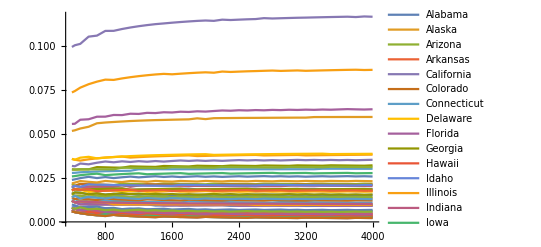

```mathematica
fractionOfElectors=(r|->Prepend[(N[#/r[["total"]],6])&/@KeyDrop[r,{"total","n"}],"n"->r[["n"]]])/@numberOfElectors;
ListPlot[Transpose[KeyDrop[(r|->({r[["n"]],#}&/@r))/@fractionOfElectors,{"n"}]],Joined->True,PlotRange->All]
```

### Plain Relative Proportionality

If we want, we can compare fraction of the population to fraction of the.
But note this is a bad measure, as the electors don’t get to free vote. We’ll get into better ways to measure voting power in the next section.

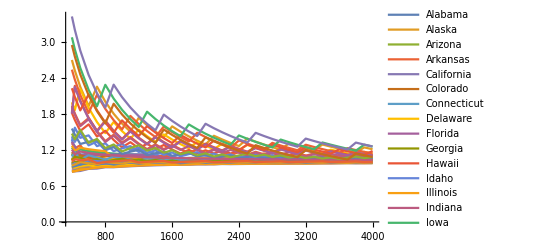

```mathematica
relativeProportionalityCoords=Dataset[(r|->
Merge[
{KeyDrop[r,{"total","n"}],Association@((#[[1]]->#[[2]])&/@usa50StateAndDCPopFraction)},
{r[["n"]],#[[1]]/#[[2]]}&
]
)/@fractionOfElectors];
ListPlot[Transpose[relativeProportionalityCoords],Joined->True,PlotRange->All,PlotLegends->Automatic]
```

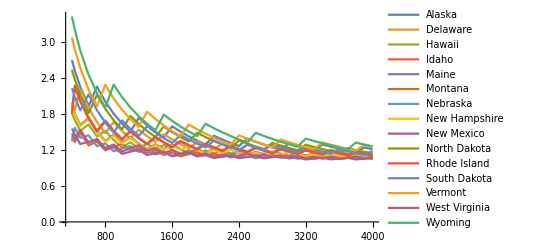

```mathematica
relativeProportionalityCoords=Dataset[(r|->
Merge[
{KeyDrop[r,{"total","n"}],Association@((#[[1]]->#[[2]])&/@usa50StateAndDCPopFraction)},
{r[["n"]],#[[1]]/#[[2]]}&
]
)/@fractionOfElectors];
ListPlot[
KeySelect[Transpose[relativeProportionalityCoords],MemberQ[smallest15States,#]&],
Joined->True,PlotRange->All,PlotLegends->Automatic]
```

## Electoral Power

Now, the problem with this is we can’t just take the fraction, and divide it by the population of each state, and say “this is unfair because the proportion of electors is not equal to the proportion of population” because all states (except Maine and Nebraska) vote at large; that is every elector for that state votes for the single winner for their state.
  Thus in fact the correct way to analyse this problem is as a system of majority voting where the participants (the states) have differently weighted votes.

### Indices of Power

#### Banzhaf Index

```mathematica
(* Uno's algorithm for computing the Banzhaf index.
(Takeaki Uno, 2012, Efficient Computation of Power Indices for Weighted Majority Games) *)
BanzhafIndex=Function[ws,
Module[{quota,maxcol,iws,l,u,usum,out},
quota=Ceiling[(Total[ws]+1)/2];
(* As the update steps for l and u only 'reach back' by the maximum weight less than or equal to the quota, this quantity bounds the total length of rows. An appropriate bound is to assume that the maximum weight is used on every step, thus we get Length[ws] increases of the maximum weight at the final row. *);
maxcol=Min[quota-1,Length[ws]*Max[Select[ws,#<=quota&]]];
l=#[[1]]&/@NestWhileList[
ri|->Module[{r,i},
{r,i}=ri;
{Table[
r[[y+1]]+If[y<ws[[i]],0,r[[y-ws[[i]]+1]]],
{y,0,maxcol}
],
i+1}
],
{Table[Boole[y==0],{y,0,maxcol}],1},
ri|->ri[[2]]<Length[ws]
];
u=Reverse[#[[1]]&/@NestWhileList[
ri|->Module[{r,i},
{r,i}=ri;
{Table[
r[[y+1]]+If[y<ws[[i]],0,r[[y-ws[[i]]+1]]],
{y,0,maxcol}
],i-1}
],
{Table[Boole[y==0],{y,0,maxcol}],Length[ws]},
ri|->1<ri[[2]]
]];
usum=FoldList[Plus,Table[0,{x,1,Length[u]}],Transpose[u]];
Table[
Sum[
l[[i,z+1]]*(usum[[Min[quota-z,maxcol+1]+1,i]]-usum[[Min[Max[quota-ws[[i]]-z,0],maxcol+1]+1,i]]),
{z,0,maxcol}
],
{i,1,Length[ws]}
]
]
];
```

```mathematica
BanzhafIndex[{1,1,4,6}]
```

{1,1,1,7}

```mathematica
(* The Banzhaf index of a vector of all 1s; same for all entries, so it just returns the number.
Recall that the Banzhaf index of voter i is the number of coalitions (subsets) which meet quota, but would not meet quota if i was removed. Recall the quota is Ceiling[(n+1)/2].
As i contributes 1, the number of coalitions which meet quota, for which i is decisive is the subsets which are of size Ceiling[(n+1)/2]-1, chosen from all voters except i (i.e. n-1 of them).
Note that Ceiling[(n+1)/2]-1 == Floor[n/2] for the integers.
*)
UniformBanzhafIndex=Function[n,Binomial[n-1,Floor[(n-1)/2]]];
```

```mathematica
(* Even: k=2*n, Binomial[2*n-1,n - 1] = Prod[(2n-i)/i,{i,1,n-1}] = ((2n-1)!)/((n-1)!(n)!)
Odd: k=2*n+1, Binomial[2*n,n] = Prod[(2n+1-i)/i,{i,1,n}] = ((2n)!)/(n!)^2
*)
```

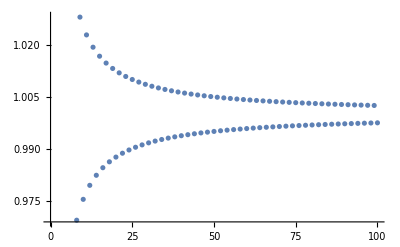

```mathematica
(* Unfortunately, the binomial function is very slow to calculate for large numbers (like the population of a state).
Thus here we use the approximation Binomial[2n,n] ~ 2^(2n)/Sqrt[n Pi].
*)
UniformAbsoluteBanzhafIndexApproximation=Function[n,1/(√(2*π*n))];
ListPlot[Table[{n,(UniformBanzhafIndex[n]/2^n)/UniformAbsoluteBanzhafIndexApproximation[n]},{n,1,100,1}]]
```

For example, the error at the number of population in the smallest state (Wyoming) is about 2×10^-10, and the error decreases as the number gets larger. The probabilities that come out of our problem are small, but still orders of magnitude larger than that, so it’s perfectly fine to use it for our problem.

```mathematica
N[UniformAbsoluteBanzhafIndexApproximation[577605]-UniformBanzhafIndex[577605]/2^577605]
```

-2.27198×10^-10

### Power per State

#### Banzhaf Index

```mathematica
electorsBanzhafCount=(r|->
Module[{n,states,electors,bzfidx},
{n,states}=r;
electors=#[[2]]&/@states;
bzfidx=BanzhafIndex[electors];
{n,Length[electors],Association@MapThread[#1[[1]]->#2&,{states,bzfidx}]}
]
)/@electorsAtDifferentSizes;
```

```mathematica
electorsAbsoluteBanzhafIndex=Association@@(#[[1]]->(c|->c/2^(#[[2]]))/@#[[3]]&/@electorsBanzhafCount);
electorsNormalisedBanzhafIndex={#[[1]],(c|->c/Total[#[[3]]])/@#[[3]]}&/@electorsBanzhafCount;
```

Now, we can compare the relative proportionality of the size of the state to its power to affect the outcome of the vote.

```mathematica
relativePowerProportionalityCoords=Dataset[(r|->
Merge[
{r[[2]],Association@((#[[1]]->#[[2]])&/@usa50StateAndDCPopFraction)},
{r[[1]],#[[1]]/#[[2]]}&
]
)/@electorsNormalisedBanzhafIndex];
```

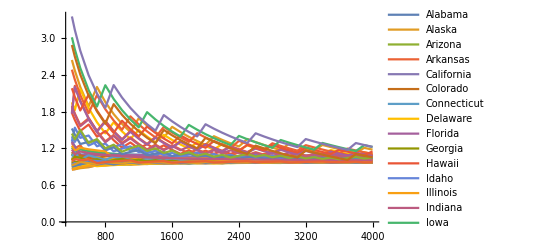

```mathematica
ListPlot[
Transpose[relativePowerProportionalityCoords],
Joined->True,PlotRange->All
]
```

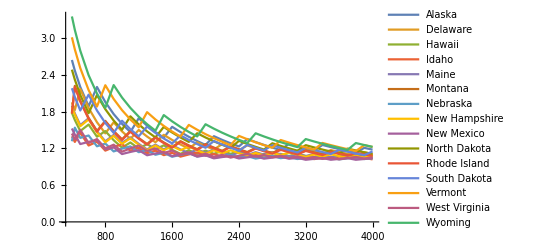

```mathematica
ListPlot[
KeySelect[Transpose[relativePowerProportionalityCoords],MemberQ[smallest15States,#]&],
Joined->True,PlotRange->All
]
```

```mathematica
totalPop50StatesAndDC
```

331511512

### Power per Voter in a State

What is the probability that any particular voter is in a coalition that is decisive, and that voter is decisive?

```mathematica
uniformVoterDecisiveProbability=UniformAbsoluteBanzhafIndexApproximation[usaVotersTotal];
```

```mathematica
N[uniformVoterDecisiveProbability]
```

0.0000316951

```mathematica
voterInStateDecisiveProbability=
(r|->
Merge[{r,usaStateVoters},#[[1]]*UniformAbsoluteBanzhafIndexApproximation[#[[2]]]&]
)/@electorsAbsoluteBanzhafIndex;
```

```mathematica
voterInStateDecisiveProbabilityCoords=
Dataset[KeyValueMap[
({n,r}|->{n,#}&/@r),
voterInStateDecisiveProbability
]];
```

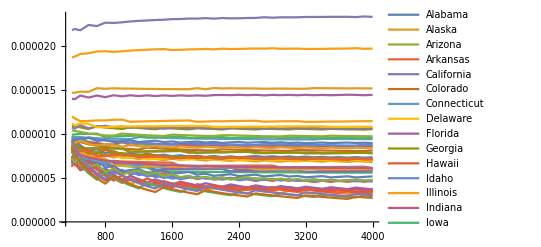

```mathematica
ListPlot[
Transpose[voterInStateDecisiveProbabilityCoords],
Joined->True,PlotRange->All
]
```

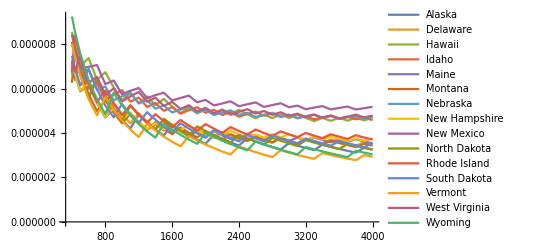

```mathematica
ListPlot[
KeySelect[Transpose[voterInStateDecisiveProbabilityCoords],MemberQ[smallest15States,#]&],
Joined->True,PlotRange->All
]
```

```mathematica
ListPlot[
KeySelect[Transpose[voterInStateDecisiveProbabilityCoords],MemberQ[largest5Smallest5States,#]&],
Joined->True,PlotRange->All,PlotLegends->Automatic
]
```

Voter Decisive Vote Probability of the 5 Largest and 5 Smallest States

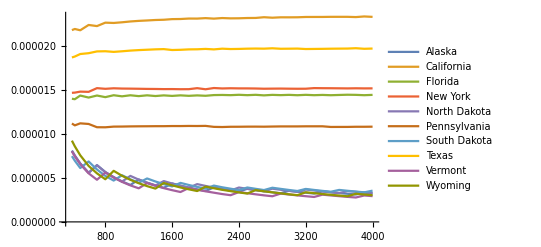

```mathematica
comparativeVoterInStateDecisiveProbability=
(r|->Outer[N[#1/#2,3]&,Values[r],Values[r]])/@voterInStateDecisiveProbability;
```

```mathematica
Max[Max/@comparativeVoterInStateDecisiveProbability[435]]
```

3.45

```mathematica
{
Keys[voterInStateDecisiveProbability[435]][[Ordering[Max/@comparativeVoterInStateDecisiveProbability[435],1][[1]]]],
Keys[voterInStateDecisiveProbability[435]][[Ordering[Min/@comparativeVoterInStateDecisiveProbability[435],-1][[1]]]]
}
```

{Delaware,California}

```mathematica
TableForm[
comparativeVoterInStateDecisiveProbability[435],
TableHeadings->{Keys[voterInStateDecisiveProbability[435]],Keys[voterInStateDecisiveProbability[435]]}
]
```

| Alabama | Alaska | Arizona | Arkansas | California | Colorado | Connecticut | Delaware | Florida | Georgia | Hawaii | Idaho | Illinois | Indiana | Iowa | Kansas | Kentucky | Louisiana | Maine | Maryland | Massachusetts | Michigan | Minnesota | Mississippi | Missouri | Montana | Nebraska | Nevada | New Hampshire | New Jersey | New Mexico | New York | North Carolina | North Dakota | Ohio | Oklahoma | Oregon | Pennsylvania | Rhode Island | South Carolina | South Dakota | Tennessee | Texas | Utah | Vermont | Virginia | Washington | West Virginia | Wisconsin | Wyoming | District of Columbia
Alabama | 1. | 1.18 | 0.987 | 1.09 | 0.406 | 1.07 | 1.14 | 1.4 | 0.639 | 0.821 | 1.12 | 1.38 | 0.757 | 0.934 | 1.28 | 1.15 | 1.08 | 1.08 | 1.34 | 1.03 | 1.02 | 0.923 | 1.07 | 1.13 | 1.03 | 1.15 | 1.16 | 1.17 | 1.33 | 0.897 | 1.14 | 0.606 | 0.863 | 1.19 | 0.84 | 1.05 | 1.14 | 0.812 | 1.06 | 1.04 | 1.28 | 0.937 | 0.474 | 1.2 | 1.2 | 0.957 | 0.993 | 1.32 | 1.07 | 1.04 | 1.16
Alaska | 0.846 | 1. | 0.835 | 0.92 | 0.344 | 0.901 | 0.964 | 1.18 | 0.54 | 0.694 | 0.948 | 1.17 | 0.64 | 0.79 | 1.08 | 0.977 | 0.913 | 0.915 | 1.13 | 0.87 | 0.864 | 0.78 | 0.903 | 0.955 | 0.868 | 0.972 | 0.978 | 0.988 | 1.12 | 0.758 | 0.961 | 0.513 | 0.73 | 1. | 0.711 | 0.892 | 0.962 | 0.687 | 0.9 | 0.88 | 1.08 | 0.792 | 0.401 | 1.02 | 1.01 | 0.809 | 0.84 | 1.11 | 0.906 | 0.877 | 0.979
Arizona | 1.01 | 1.2 | 1. | 1.1 | 0.412 | 1.08 | 1.16 | 1.42 | 0.648 | 0.832 | 1.14 | 1.4 | 0.767 | 0.946 | 1.3 | 1.17 | 1.09 | 1.1 | 1.36 | 1.04 | 1.04 | 0.935 | 1.08 | 1.14 | 1.04 | 1.16 | 1.17 | 1.18 | 1.35 | 0.909 | 1.15 | 0.614 | 0.875 | 1.2 | 0.852 | 1.07 | 1.15 | 0.823 | 1.08 | 1.05 | 1.3 | 0.95 | 0.48 | 1.22 | 1.21 | 0.97 | 1.01 | 1.34 | 1.09 | 1.05 | 1.17
Arkansas | 0.919 | 1.09 | 0.907 | 1. | 0.374 | 0.979 | 1.05 | 1.29 | 0.587 | 0.755 | 1.03 | 1.27 | 0.696 | 0.858 | 1.18 | 1.06 | 0.992 | 0.995 | 1.23 | 0.945 | 0.939 | 0.848 | 0.982 | 1.04 | 0.944 | 1.06 | 1.06 | 1.07 | 1.22 | 0.824 | 1.05 | 0.557 | 0.793 | 1.09 | 0.772 | 0.969 | 1.05 | 0.746 | 0.978 | 0.956 | 1.18 | 0.861 | 0.436 | 1.1 | 1.1 | 0.88 | 0.913 | 1.21 | 0.985 | 0.954 | 1.06
California | 2.46 | 2.91 | 2.43 | 2.68 | 1. | 2.62 | 2.81 | 3.45 | 1.57 | 2.02 | 2.76 | 3.39 | 1.86 | 2.3 | 3.15 | 2.84 | 2.66 | 2.66 | 3.29 | 2.53 | 2.51 | 2.27 | 2.63 | 2.78 | 2.53 | 2.83 | 2.85 | 2.87 | 3.27 | 2.21 | 2.8 | 1.49 | 2.12 | 2.92 | 2.07 | 2.6 | 2.8 | 2. | 2.62 | 2.56 | 3.15 | 2.31 | 1.17 | 2.96 | 2.94 | 2.35 | 2.44 | 3.24 | 2.64 | 2.55 | 2.85
Colorado | 0.939 | 1.11 | 0.927 | 1.02 | 0.382 | 1. | 1.07 | 1.32 | 0.6 | 0.771 | 1.05 | 1.29 | 0.711 | 0.877 | 1.2 | 1.08 | 1.01 | 1.02 | 1.26 | 0.966 | 0.959 | 0.866 | 1. | 1.06 | 0.964 | 1.08 | 1.09 | 1.1 | 1.25 | 0.842 | 1.07 | 0.569 | 0.81 | 1.11 | 0.789 | 0.99 | 1.07 | 0.762 | 0.999 | 0.977 | 1.2 | 0.88 | 0.445 | 1.13 | 1.12 | 0.898 | 0.932 | 1.24 | 1.01 | 0.974 | 1.09
Connecticut | 0.877 | 1.04 | 0.866 | 0.954 | 0.356 | 0.934 | 1. | 1.23 | 0.56 | 0.72 | 0.983 | 1.21 | 0.664 | 0.819 | 1.12 | 1.01 | 0.947 | 0.949 | 1.17 | 0.902 | 0.896 | 0.809 | 0.937 | 0.991 | 0.9 | 1.01 | 1.01 | 1.02 | 1.16 | 0.786 | 0.997 | 0.532 | 0.757 | 1.04 | 0.737 | 0.925 | 0.998 | 0.712 | 0.933 | 0.912 | 1.12 | 0.822 | 0.416 | 1.05 | 1.05 | 0.839 | 0.871 | 1.16 | 0.94 | 0.91 | 1.01
Delaware | 0.714 | 0.844 | 0.705 | 0.777 | 0.29 | 0.76 | 0.814 | 1. | 0.456 | 0.586 | 0.8 | 0.984 | 0.541 | 0.667 | 0.915 | 0.825 | 0.771 | 0.773 | 0.956 | 0.734 | 0.73 | 0.659 | 0.763 | 0.806 | 0.733 | 0.82 | 0.826 | 0.834 | 0.948 | 0.64 | 0.812 | 0.433 | 0.616 | 0.847 | 0.6 | 0.753 | 0.812 | 0.58 | 0.76 | 0.743 | 0.915 | 0.669 | 0.338 | 0.858 | 0.854 | 0.683 | 0.709 | 0.941 | 0.765 | 0.741 | 0.826
Florida | 1.56 | 1.85 | 1.54 | 1.7 | 0.636 | 1.67 | 1.78 | 2.19 | 1. | 1.29 | 1.75 | 2.16 | 1.19 | 1.46 | 2.01 | 1.81 | 1.69 | 1.69 | 2.09 | 1.61 | 1.6 | 1.44 | 1.67 | 1.77 | 1.61 | 1.8 | 1.81 | 1.83 | 2.08 | 1.4 | 1.78 | 0.949 | 1.35 | 1.86 | 1.32 | 1.65 | 1.78 | 1.27 | 1.67 | 1.63 | 2.01 | 1.47 | 0.742 | 1.88 | 1.87 | 1.5 | 1.55 | 2.06 | 1.68 | 1.62 | 1.81
Georgia | 1.22 | 1.44 | 1.2 | 1.32 | 0.495 | 1.3 | 1.39 | 1.71 | 0.778 | 1. | 1.36 | 1.68 | 0.922 | 1.14 | 1.56 | 1.41 | 1.31 | 1.32 | 1.63 | 1.25 | 1.24 | 1.12 | 1.3 | 1.38 | 1.25 | 1.4 | 1.41 | 1.42 | 1.62 | 1.09 | 1.38 | 0.738 | 1.05 | 1.45 | 1.02 | 1.28 | 1.39 | 0.989 | 1.3 | 1.27 | 1.56 | 1.14 | 0.577 | 1.46 | 1.46 | 1.17 | 1.21 | 1.61 | 1.31 | 1.26 | 1.41
Hawaii | 0.892 | 1.06 | 0.88 | 0.971 | 0.363 | 0.95 | 1.02 | 1.25 | 0.57 | 0.733 | 1. | 1.23 | 0.676 | 0.833 | 1.14 | 1.03 | 0.963 | 0.966 | 1.19 | 0.918 | 0.912 | 0.823 | 0.953 | 1.01 | 0.916 | 1.03 | 1.03 | 1.04 | 1.18 | 0.8 | 1.01 | 0.541 | 0.77 | 1.06 | 0.75 | 0.941 | 1.02 | 0.724 | 0.949 | 0.928 | 1.14 | 0.836 | 0.423 | 1.07 | 1.07 | 0.854 | 0.886 | 1.18 | 0.956 | 0.926 | 1.03
Idaho | 0.726 | 0.858 | 0.716 | 0.79 | 0.295 | 0.773 | 0.828 | 1.02 | 0.464 | 0.596 | 0.814 | 1. | 0.55 | 0.678 | 0.93 | 0.838 | 0.783 | 0.786 | 0.972 | 0.747 | 0.742 | 0.67 | 0.775 | 0.82 | 0.745 | 0.834 | 0.84 | 0.848 | 0.964 | 0.651 | 0.825 | 0.44 | 0.627 | 0.861 | 0.61 | 0.766 | 0.826 | 0.589 | 0.772 | 0.755 | 0.931 | 0.68 | 0.344 | 0.873 | 0.868 | 0.695 | 0.721 | 0.957 | 0.778 | 0.753 | 0.84
Illinois | 1.32 | 1.56 | 1.3 | 1.44 | 0.537 | 1.41 | 1.51 | 1.85 | 0.844 | 1.08 | 1.48 | 1.82 | 1. | 1.23 | 1.69 | 1.53 | 1.43 | 1.43 | 1.77 | 1.36 | 1.35 | 1.22 | 1.41 | 1.49 | 1.36 | 1.52 | 1.53 | 1.54 | 1.75 | 1.18 | 1.5 | 0.801 | 1.14 | 1.57 | 1.11 | 1.39 | 1.5 | 1.07 | 1.41 | 1.37 | 1.69 | 1.24 | 0.626 | 1.59 | 1.58 | 1.26 | 1.31 | 1.74 | 1.42 | 1.37 | 1.53
Indiana | 1.07 | 1.27 | 1.06 | 1.17 | 0.435 | 1.14 | 1.22 | 1.5 | 0.684 | 0.879 | 1.2 | 1.48 | 0.811 | 1. | 1.37 | 1.24 | 1.16 | 1.16 | 1.43 | 1.1 | 1.09 | 0.988 | 1.14 | 1.21 | 1.1 | 1.23 | 1.24 | 1.25 | 1.42 | 0.96 | 1.22 | 0.649 | 0.924 | 1.27 | 0.9 | 1.13 | 1.22 | 0.87 | 1.14 | 1.11 | 1.37 | 1. | 0.508 | 1.29 | 1.28 | 1.02 | 1.06 | 1.41 | 1.15 | 1.11 | 1.24
Iowa | 0.78 | 0.923 | 0.77 | 0.849 | 0.317 | 0.831 | 0.89 | 1.09 | 0.499 | 0.641 | 0.875 | 1.08 | 0.591 | 0.729 | 1. | 0.901 | 0.842 | 0.845 | 1.04 | 0.803 | 0.797 | 0.72 | 0.834 | 0.881 | 0.801 | 0.897 | 0.903 | 0.912 | 1.04 | 0.7 | 0.887 | 0.473 | 0.674 | 0.926 | 0.656 | 0.823 | 0.888 | 0.634 | 0.83 | 0.812 | 1. | 0.731 | 0.37 | 0.938 | 0.933 | 0.747 | 0.775 | 1.03 | 0.836 | 0.81 | 0.903
Kansas | 0.866 | 1.02 | 0.854 | 0.942 | 0.352 | 0.922 | 0.987 | 1.21 | 0.553 | 0.711 | 0.97 | 1.19 | 0.656 | 0.809 | 1.11 | 1. | 0.935 | 0.937 | 1.16 | 0.89 | 0.885 | 0.799 | 0.925 | 0.978 | 0.889 | 0.995 | 1. | 1.01 | 1.15 | 0.776 | 0.984 | 0.525 | 0.747 | 1.03 | 0.728 | 0.913 | 0.985 | 0.703 | 0.921 | 0.901 | 1.11 | 0.811 | 0.41 | 1.04 | 1.04 | 0.829 | 0.86 | 1.14 | 0.928 | 0.898 | 1.
Kentucky | 0.926 | 1.1 | 0.914 | 1.01 | 0.376 | 0.987 | 1.06 | 1.3 | 0.592 | 0.761 | 1.04 | 1.28 | 0.702 | 0.865 | 1.19 | 1.07 | 1. | 1. | 1.24 | 0.953 | 0.947 | 0.855 | 0.99 | 1.05 | 0.951 | 1.06 | 1.07 | 1.08 | 1.23 | 0.831 | 1.05 | 0.562 | 0.8 | 1.1 | 0.778 | 0.977 | 1.05 | 0.752 | 0.986 | 0.964 | 1.19 | 0.868 | 0.439 | 1.11 | 1.11 | 0.887 | 0.92 | 1.22 | 0.993 | 0.961 | 1.07
Louisiana | 0.924 | 1.09 | 0.912 | 1.01 | 0.375 | 0.984 | 1.05 | 1.29 | 0.59 | 0.759 | 1.04 | 1.27 | 0.7 | 0.863 | 1.18 | 1.07 | 0.997 | 1. | 1.24 | 0.95 | 0.944 | 0.853 | 0.987 | 1.04 | 0.949 | 1.06 | 1.07 | 1.08 | 1.23 | 0.829 | 1.05 | 0.56 | 0.798 | 1.1 | 0.776 | 0.975 | 1.05 | 0.75 | 0.983 | 0.961 | 1.18 | 0.866 | 0.438 | 1.11 | 1.1 | 0.884 | 0.918 | 1.22 | 0.99 | 0.959 | 1.07
Maine | 0.747 | 0.883 | 0.737 | 0.813 | 0.304 | 0.796 | 0.852 | 1.05 | 0.477 | 0.613 | 0.837 | 1.03 | 0.566 | 0.698 | 0.957 | 0.863 | 0.806 | 0.808 | 1. | 0.768 | 0.763 | 0.689 | 0.798 | 0.844 | 0.767 | 0.858 | 0.864 | 0.873 | 0.992 | 0.67 | 0.849 | 0.453 | 0.645 | 0.886 | 0.628 | 0.788 | 0.85 | 0.607 | 0.795 | 0.777 | 0.958 | 0.7 | 0.354 | 0.898 | 0.893 | 0.715 | 0.742 | 0.985 | 0.801 | 0.775 | 0.864
Maryland | 0.972 | 1.15 | 0.96 | 1.06 | 0.395 | 1.04 | 1.11 | 1.36 | 0.621 | 0.798 | 1.09 | 1.34 | 0.736 | 0.908 | 1.25 | 1.12 | 1.05 | 1.05 | 1.3 | 1. | 0.993 | 0.897 | 1.04 | 1.1 | 0.998 | 1.12 | 1.12 | 1.14 | 1.29 | 0.872 | 1.11 | 0.59 | 0.839 | 1.15 | 0.817 | 1.03 | 1.11 | 0.79 | 1.03 | 1.01 | 1.25 | 0.911 | 0.461 | 1.17 | 1.16 | 0.93 | 0.966 | 1.28 | 1.04 | 1.01 | 1.13
Massachusetts | 0.979 | 1.16 | 0.966 | 1.06 | 0.398 | 1.04 | 1.12 | 1.37 | 0.625 | 0.804 | 1.1 | 1.35 | 0.741 | 0.914 | 1.25 | 1.13 | 1.06 | 1.06 | 1.31 | 1.01 | 1. | 0.903 | 1.05 | 1.11 | 1. | 1.12 | 1.13 | 1.14 | 1.3 | 0.878 | 1.11 | 0.593 | 0.845 | 1.16 | 0.822 | 1.03 | 1.11 | 0.795 | 1.04 | 1.02 | 1.25 | 0.917 | 0.464 | 1.18 | 1.17 | 0.937 | 0.972 | 1.29 | 1.05 | 1.02 | 1.13
Michigan | 1.08 | 1.28 | 1.07 | 1.18 | 0.44 | 1.15 | 1.24 | 1.52 | 0.693 | 0.89 | 1.21 | 1.49 | 0.821 | 1.01 | 1.39 | 1.25 | 1.17 | 1.17 | 1.45 | 1.11 | 1.11 | 1. | 1.16 | 1.22 | 1.11 | 1.25 | 1.25 | 1.27 | 1.44 | 0.972 | 1.23 | 0.657 | 0.935 | 1.29 | 0.911 | 1.14 | 1.23 | 0.88 | 1.15 | 1.13 | 1.39 | 1.02 | 0.514 | 1.3 | 1.3 | 1.04 | 1.08 | 1.43 | 1.16 | 1.12 | 1.25
Minnesota | 0.936 | 1.11 | 0.924 | 1.02 | 0.38 | 0.997 | 1.07 | 1.31 | 0.598 | 0.769 | 1.05 | 1.29 | 0.709 | 0.874 | 1.2 | 1.08 | 1.01 | 1.01 | 1.25 | 0.963 | 0.956 | 0.864 | 1. | 1.06 | 0.961 | 1.08 | 1.08 | 1.09 | 1.24 | 0.839 | 1.06 | 0.568 | 0.808 | 1.11 | 0.787 | 0.987 | 1.07 | 0.76 | 0.996 | 0.974 | 1.2 | 0.877 | 0.444 | 1.13 | 1.12 | 0.896 | 0.93 | 1.23 | 1. | 0.971 | 1.08
Mississippi | 0.885 | 1.05 | 0.874 | 0.963 | 0.36 | 0.943 | 1.01 | 1.24 | 0.566 | 0.727 | 0.992 | 1.22 | 0.671 | 0.827 | 1.13 | 1.02 | 0.956 | 0.958 | 1.19 | 0.911 | 0.905 | 0.817 | 0.946 | 1. | 0.909 | 1.02 | 1.02 | 1.03 | 1.18 | 0.794 | 1.01 | 0.537 | 0.764 | 1.05 | 0.744 | 0.934 | 1.01 | 0.719 | 0.942 | 0.921 | 1.14 | 0.83 | 0.42 | 1.06 | 1.06 | 0.847 | 0.879 | 1.17 | 0.949 | 0.919 | 1.02
Missouri | 0.974 | 1.15 | 0.961 | 1.06 | 0.396 | 1.04 | 1.11 | 1.36 | 0.622 | 0.8 | 1.09 | 1.34 | 0.738 | 0.91 | 1.25 | 1.13 | 1.05 | 1.05 | 1.3 | 1. | 0.995 | 0.899 | 1.04 | 1.1 | 1. | 1.12 | 1.13 | 1.14 | 1.29 | 0.873 | 1.11 | 0.591 | 0.841 | 1.16 | 0.819 | 1.03 | 1.11 | 0.791 | 1.04 | 1.01 | 1.25 | 0.913 | 0.462 | 1.17 | 1.16 | 0.932 | 0.967 | 1.28 | 1.04 | 1.01 | 1.13
Montana | 0.87 | 1.03 | 0.859 | 0.947 | 0.354 | 0.927 | 0.992 | 1.22 | 0.556 | 0.715 | 0.976 | 1.2 | 0.659 | 0.813 | 1.12 | 1.01 | 0.939 | 0.942 | 1.17 | 0.895 | 0.889 | 0.803 | 0.93 | 0.983 | 0.893 | 1. | 1.01 | 1.02 | 1.16 | 0.78 | 0.989 | 0.528 | 0.751 | 1.03 | 0.731 | 0.918 | 0.99 | 0.707 | 0.926 | 0.905 | 1.12 | 0.816 | 0.413 | 1.05 | 1.04 | 0.833 | 0.864 | 1.15 | 0.933 | 0.903 | 1.01
Nebraska | 0.865 | 1.02 | 0.853 | 0.941 | 0.351 | 0.921 | 0.986 | 1.21 | 0.552 | 0.71 | 0.969 | 1.19 | 0.655 | 0.807 | 1.11 | 0.999 | 0.933 | 0.936 | 1.16 | 0.889 | 0.883 | 0.798 | 0.924 | 0.976 | 0.888 | 0.993 | 1. | 1.01 | 1.15 | 0.775 | 0.983 | 0.524 | 0.746 | 1.03 | 0.726 | 0.912 | 0.984 | 0.702 | 0.92 | 0.899 | 1.11 | 0.81 | 0.41 | 1.04 | 1.03 | 0.827 | 0.859 | 1.14 | 0.927 | 0.897 | 1.
Nevada | 0.856 | 1.01 | 0.845 | 0.931 | 0.348 | 0.912 | 0.976 | 1.2 | 0.547 | 0.703 | 0.96 | 1.18 | 0.648 | 0.799 | 1.1 | 0.989 | 0.924 | 0.927 | 1.15 | 0.88 | 0.875 | 0.79 | 0.915 | 0.967 | 0.879 | 0.984 | 0.99 | 1. | 1.14 | 0.768 | 0.973 | 0.519 | 0.739 | 1.02 | 0.719 | 0.903 | 0.974 | 0.695 | 0.911 | 0.89 | 1.1 | 0.802 | 0.406 | 1.03 | 1.02 | 0.819 | 0.85 | 1.13 | 0.918 | 0.888 | 0.991
New Hampshire | 0.753 | 0.891 | 0.743 | 0.819 | 0.306 | 0.802 | 0.859 | 1.05 | 0.481 | 0.618 | 0.844 | 1.04 | 0.57 | 0.703 | 0.965 | 0.87 | 0.813 | 0.815 | 1.01 | 0.775 | 0.77 | 0.695 | 0.805 | 0.851 | 0.773 | 0.865 | 0.871 | 0.88 | 1. | 0.675 | 0.856 | 0.457 | 0.65 | 0.894 | 0.633 | 0.794 | 0.857 | 0.612 | 0.801 | 0.783 | 0.966 | 0.706 | 0.357 | 0.905 | 0.9 | 0.721 | 0.748 | 0.993 | 0.807 | 0.781 | 0.872
New Jersey | 1.12 | 1.32 | 1.1 | 1.21 | 0.453 | 1.19 | 1.27 | 1.56 | 0.713 | 0.916 | 1.25 | 1.54 | 0.845 | 1.04 | 1.43 | 1.29 | 1.2 | 1.21 | 1.49 | 1.15 | 1.14 | 1.03 | 1.19 | 1.26 | 1.14 | 1.28 | 1.29 | 1.3 | 1.48 | 1. | 1.27 | 0.676 | 0.963 | 1.32 | 0.937 | 1.18 | 1.27 | 0.906 | 1.19 | 1.16 | 1.43 | 1.04 | 0.529 | 1.34 | 1.33 | 1.07 | 1.11 | 1.47 | 1.2 | 1.16 | 1.29
New Mexico | 0.88 | 1.04 | 0.868 | 0.957 | 0.357 | 0.937 | 1. | 1.23 | 0.562 | 0.722 | 0.986 | 1.21 | 0.666 | 0.821 | 1.13 | 1.02 | 0.949 | 0.952 | 1.18 | 0.905 | 0.899 | 0.812 | 0.94 | 0.993 | 0.903 | 1.01 | 1.02 | 1.03 | 1.17 | 0.789 | 1. | 0.533 | 0.759 | 1.04 | 0.739 | 0.928 | 1. | 0.714 | 0.936 | 0.915 | 1.13 | 0.824 | 0.417 | 1.06 | 1.05 | 0.842 | 0.873 | 1.16 | 0.943 | 0.913 | 1.02
New York | 1.65 | 1.95 | 1.63 | 1.79 | 0.67 | 1.76 | 1.88 | 2.31 | 1.05 | 1.35 | 1.85 | 2.27 | 1.25 | 1.54 | 2.11 | 1.9 | 1.78 | 1.78 | 2.21 | 1.7 | 1.69 | 1.52 | 1.76 | 1.86 | 1.69 | 1.89 | 1.91 | 1.93 | 2.19 | 1.48 | 1.87 | 1. | 1.42 | 1.96 | 1.39 | 1.74 | 1.88 | 1.34 | 1.75 | 1.72 | 2.11 | 1.55 | 0.782 | 1.98 | 1.97 | 1.58 | 1.64 | 2.17 | 1.77 | 1.71 | 1.91
North Carolina | 1.16 | 1.37 | 1.14 | 1.26 | 0.471 | 1.23 | 1.32 | 1.62 | 0.74 | 0.951 | 1.3 | 1.6 | 0.877 | 1.08 | 1.48 | 1.34 | 1.25 | 1.25 | 1.55 | 1.19 | 1.18 | 1.07 | 1.24 | 1.31 | 1.19 | 1.33 | 1.34 | 1.35 | 1.54 | 1.04 | 1.32 | 0.702 | 1. | 1.37 | 0.974 | 1.22 | 1.32 | 0.941 | 1.23 | 1.2 | 1.49 | 1.09 | 0.549 | 1.39 | 1.38 | 1.11 | 1.15 | 1.53 | 1.24 | 1.2 | 1.34
North Dakota | 0.843 | 0.997 | 0.832 | 0.917 | 0.342 | 0.898 | 0.961 | 1.18 | 0.539 | 0.692 | 0.945 | 1.16 | 0.638 | 0.787 | 1.08 | 0.973 | 0.91 | 0.912 | 1.13 | 0.867 | 0.861 | 0.778 | 0.9 | 0.952 | 0.865 | 0.968 | 0.975 | 0.984 | 1.12 | 0.756 | 0.958 | 0.511 | 0.727 | 1. | 0.708 | 0.889 | 0.959 | 0.684 | 0.897 | 0.877 | 1.08 | 0.79 | 0.4 | 1.01 | 1.01 | 0.806 | 0.837 | 1.11 | 0.903 | 0.874 | 0.975
Ohio | 1.19 | 1.41 | 1.17 | 1.29 | 0.484 | 1.27 | 1.36 | 1.67 | 0.76 | 0.977 | 1.33 | 1.64 | 0.901 | 1.11 | 1.52 | 1.37 | 1.28 | 1.29 | 1.59 | 1.22 | 1.22 | 1.1 | 1.27 | 1.34 | 1.22 | 1.37 | 1.38 | 1.39 | 1.58 | 1.07 | 1.35 | 0.722 | 1.03 | 1.41 | 1. | 1.26 | 1.35 | 0.966 | 1.27 | 1.24 | 1.53 | 1.12 | 0.564 | 1.43 | 1.42 | 1.14 | 1.18 | 1.57 | 1.28 | 1.23 | 1.38
Oklahoma | 0.948 | 1.12 | 0.936 | 1.03 | 0.385 | 1.01 | 1.08 | 1.33 | 0.606 | 0.779 | 1.06 | 1.31 | 0.718 | 0.885 | 1.21 | 1.1 | 1.02 | 1.03 | 1.27 | 0.975 | 0.969 | 0.875 | 1.01 | 1.07 | 0.973 | 1.09 | 1.1 | 1.11 | 1.26 | 0.85 | 1.08 | 0.575 | 0.818 | 1.13 | 0.797 | 1. | 1.08 | 0.77 | 1.01 | 0.986 | 1.22 | 0.888 | 0.449 | 1.14 | 1.13 | 0.907 | 0.942 | 1.25 | 1.02 | 0.984 | 1.1
Oregon | 0.879 | 1.04 | 0.867 | 0.956 | 0.357 | 0.936 | 1. | 1.23 | 0.562 | 0.722 | 0.985 | 1.21 | 0.666 | 0.821 | 1.13 | 1.02 | 0.949 | 0.951 | 1.18 | 0.904 | 0.898 | 0.811 | 0.939 | 0.993 | 0.902 | 1.01 | 1.02 | 1.03 | 1.17 | 0.788 | 0.999 | 0.533 | 0.759 | 1.04 | 0.739 | 0.927 | 1. | 0.714 | 0.935 | 0.914 | 1.13 | 0.823 | 0.417 | 1.06 | 1.05 | 0.841 | 0.873 | 1.16 | 0.942 | 0.912 | 1.02
Pennsylvania | 1.23 | 1.46 | 1.22 | 1.34 | 0.5 | 1.31 | 1.4 | 1.72 | 0.787 | 1.01 | 1.38 | 1.7 | 0.933 | 1.15 | 1.58 | 1.42 | 1.33 | 1.33 | 1.65 | 1.27 | 1.26 | 1.14 | 1.32 | 1.39 | 1.26 | 1.41 | 1.42 | 1.44 | 1.64 | 1.1 | 1.4 | 0.747 | 1.06 | 1.46 | 1.03 | 1.3 | 1.4 | 1. | 1.31 | 1.28 | 1.58 | 1.15 | 0.584 | 1.48 | 1.47 | 1.18 | 1.22 | 1.62 | 1.32 | 1.28 | 1.43
Rhode Island | 0.94 | 1.11 | 0.927 | 1.02 | 0.382 | 1. | 1.07 | 1.32 | 0.601 | 0.772 | 1.05 | 1.29 | 0.712 | 0.878 | 1.2 | 1.09 | 1.01 | 1.02 | 1.26 | 0.967 | 0.96 | 0.867 | 1. | 1.06 | 0.965 | 1.08 | 1.09 | 1.1 | 1.25 | 0.843 | 1.07 | 0.57 | 0.811 | 1.12 | 0.79 | 0.991 | 1.07 | 0.763 | 1. | 0.977 | 1.2 | 0.881 | 0.446 | 1.13 | 1.12 | 0.899 | 0.933 | 1.24 | 1.01 | 0.975 | 1.09
South Carolina | 0.961 | 1.14 | 0.949 | 1.05 | 0.391 | 1.02 | 1.1 | 1.35 | 0.614 | 0.789 | 1.08 | 1.32 | 0.728 | 0.898 | 1.23 | 1.11 | 1.04 | 1.04 | 1.29 | 0.989 | 0.982 | 0.887 | 1.03 | 1.09 | 0.987 | 1.1 | 1.11 | 1.12 | 1.28 | 0.862 | 1.09 | 0.583 | 0.83 | 1.14 | 0.808 | 1.01 | 1.09 | 0.781 | 1.02 | 1. | 1.23 | 0.901 | 0.456 | 1.16 | 1.15 | 0.92 | 0.955 | 1.27 | 1.03 | 0.998 | 1.11
South Dakota | 0.78 | 0.922 | 0.77 | 0.849 | 0.317 | 0.831 | 0.889 | 1.09 | 0.498 | 0.64 | 0.874 | 1.07 | 0.591 | 0.728 | 0.999 | 0.901 | 0.842 | 0.844 | 1.04 | 0.802 | 0.797 | 0.72 | 0.833 | 0.881 | 0.801 | 0.896 | 0.902 | 0.911 | 1.04 | 0.699 | 0.887 | 0.473 | 0.673 | 0.926 | 0.655 | 0.823 | 0.888 | 0.633 | 0.83 | 0.811 | 1. | 0.731 | 0.37 | 0.938 | 0.932 | 0.746 | 0.775 | 1.03 | 0.836 | 0.809 | 0.903
Tennessee | 1.07 | 1.26 | 1.05 | 1.16 | 0.434 | 1.14 | 1.22 | 1.49 | 0.682 | 0.876 | 1.2 | 1.47 | 0.808 | 0.997 | 1.37 | 1.23 | 1.15 | 1.16 | 1.43 | 1.1 | 1.09 | 0.985 | 1.14 | 1.21 | 1.1 | 1.23 | 1.23 | 1.25 | 1.42 | 0.957 | 1.21 | 0.647 | 0.921 | 1.27 | 0.897 | 1.13 | 1.21 | 0.867 | 1.14 | 1.11 | 1.37 | 1. | 0.506 | 1.28 | 1.28 | 1.02 | 1.06 | 1.41 | 1.14 | 1.11 | 1.24
Texas | 2.11 | 2.49 | 2.08 | 2.29 | 0.857 | 2.25 | 2.41 | 2.95 | 1.35 | 1.73 | 2.36 | 2.91 | 1.6 | 1.97 | 2.7 | 2.44 | 2.28 | 2.28 | 2.82 | 2.17 | 2.16 | 1.95 | 2.25 | 2.38 | 2.17 | 2.42 | 2.44 | 2.46 | 2.8 | 1.89 | 2.4 | 1.28 | 1.82 | 2.5 | 1.77 | 2.22 | 2.4 | 1.71 | 2.24 | 2.19 | 2.7 | 1.98 | 1. | 2.54 | 2.52 | 2.02 | 2.09 | 2.78 | 2.26 | 2.19 | 2.44
Utah | 0.832 | 0.984 | 0.821 | 0.905 | 0.338 | 0.886 | 0.949 | 1.17 | 0.532 | 0.683 | 0.932 | 1.15 | 0.63 | 0.777 | 1.07 | 0.961 | 0.898 | 0.9 | 1.11 | 0.856 | 0.85 | 0.768 | 0.889 | 0.94 | 0.854 | 0.956 | 0.962 | 0.972 | 1.1 | 0.746 | 0.946 | 0.504 | 0.718 | 0.987 | 0.699 | 0.877 | 0.947 | 0.676 | 0.885 | 0.865 | 1.07 | 0.779 | 0.394 | 1. | 0.994 | 0.796 | 0.826 | 1.1 | 0.892 | 0.863 | 0.963
Vermont | 0.837 | 0.989 | 0.826 | 0.91 | 0.34 | 0.891 | 0.954 | 1.17 | 0.535 | 0.687 | 0.938 | 1.15 | 0.634 | 0.781 | 1.07 | 0.966 | 0.903 | 0.905 | 1.12 | 0.86 | 0.855 | 0.772 | 0.894 | 0.945 | 0.859 | 0.961 | 0.968 | 0.977 | 1.11 | 0.75 | 0.951 | 0.507 | 0.722 | 0.993 | 0.703 | 0.882 | 0.952 | 0.679 | 0.89 | 0.87 | 1.07 | 0.784 | 0.397 | 1.01 | 1. | 0.8 | 0.831 | 1.1 | 0.897 | 0.868 | 0.968
Virginia | 1.05 | 1.24 | 1.03 | 1.14 | 0.425 | 1.11 | 1.19 | 1.46 | 0.668 | 0.858 | 1.17 | 1.44 | 0.791 | 0.976 | 1.34 | 1.21 | 1.13 | 1.13 | 1.4 | 1.07 | 1.07 | 0.964 | 1.12 | 1.18 | 1.07 | 1.2 | 1.21 | 1.22 | 1.39 | 0.937 | 1.19 | 0.634 | 0.902 | 1.24 | 0.878 | 1.1 | 1.19 | 0.849 | 1.11 | 1.09 | 1.34 | 0.979 | 0.495 | 1.26 | 1.25 | 1. | 1.04 | 1.38 | 1.12 | 1.08 | 1.21
Washington | 1.01 | 1.19 | 0.994 | 1.1 | 0.409 | 1.07 | 1.15 | 1.41 | 0.643 | 0.827 | 1.13 | 1.39 | 0.763 | 0.94 | 1.29 | 1.16 | 1.09 | 1.09 | 1.35 | 1.04 | 1.03 | 0.929 | 1.08 | 1.14 | 1.03 | 1.16 | 1.16 | 1.18 | 1.34 | 0.903 | 1.14 | 0.611 | 0.869 | 1.19 | 0.846 | 1.06 | 1.15 | 0.818 | 1.07 | 1.05 | 1.29 | 0.944 | 0.477 | 1.21 | 1.2 | 0.964 | 1. | 1.33 | 1.08 | 1.04 | 1.17
West Virginia | 0.759 | 0.897 | 0.749 | 0.825 | 0.308 | 0.808 | 0.865 | 1.06 | 0.485 | 0.623 | 0.85 | 1.05 | 0.574 | 0.708 | 0.972 | 0.876 | 0.819 | 0.821 | 1.02 | 0.78 | 0.775 | 0.7 | 0.81 | 0.857 | 0.779 | 0.872 | 0.877 | 0.886 | 1.01 | 0.68 | 0.862 | 0.46 | 0.655 | 0.9 | 0.637 | 0.8 | 0.863 | 0.616 | 0.807 | 0.789 | 0.972 | 0.711 | 0.36 | 0.912 | 0.907 | 0.726 | 0.753 | 1. | 0.813 | 0.787 | 0.878
Wisconsin | 0.933 | 1.1 | 0.921 | 1.02 | 0.379 | 0.994 | 1.06 | 1.31 | 0.596 | 0.766 | 1.05 | 1.29 | 0.707 | 0.871 | 1.2 | 1.08 | 1.01 | 1.01 | 1.25 | 0.96 | 0.953 | 0.861 | 0.997 | 1.05 | 0.958 | 1.07 | 1.08 | 1.09 | 1.24 | 0.837 | 1.06 | 0.566 | 0.805 | 1.11 | 0.784 | 0.984 | 1.06 | 0.758 | 0.993 | 0.97 | 1.2 | 0.874 | 0.442 | 1.12 | 1.12 | 0.893 | 0.927 | 1.23 | 1. | 0.968 | 1.08
Wyoming | 0.964 | 1.14 | 0.951 | 1.05 | 0.392 | 1.03 | 1.1 | 1.35 | 0.616 | 0.791 | 1.08 | 1.33 | 0.73 | 0.9 | 1.23 | 1.11 | 1.04 | 1.04 | 1.29 | 0.991 | 0.985 | 0.889 | 1.03 | 1.09 | 0.989 | 1.11 | 1.11 | 1.13 | 1.28 | 0.864 | 1.1 | 0.584 | 0.832 | 1.14 | 0.81 | 1.02 | 1.1 | 0.783 | 1.03 | 1. | 1.24 | 0.903 | 0.457 | 1.16 | 1.15 | 0.922 | 0.957 | 1.27 | 1.03 | 1. | 1.12
District of Columbia | 0.864 | 1.02 | 0.853 | 0.94 | 0.351 | 0.92 | 0.985 | 1.21 | 0.552 | 0.71 | 0.969 | 1.19 | 0.654 | 0.807 | 1.11 | 0.998 | 0.933 | 0.935 | 1.16 | 0.889 | 0.883 | 0.797 | 0.923 | 0.976 | 0.887 | 0.993 | 0.999 | 1.01 | 1.15 | 0.775 | 0.982 | 0.524 | 0.746 | 1.03 | 0.726 | 0.911 | 0.983 | 0.702 | 0.919 | 0.899 | 1.11 | 0.81 | 0.41 | 1.04 | 1.03 | 0.827 | 0.858 | 1.14 | 0.926 | 0.897 | 1.

```mathematica
relativeVoterInStateDecisiveProbability=Dataset[
(nr|->
Merge[{
nr[[2]],
Association@(Apply[Rule]/@usa50StateAndDCPopData)
},{nr[[1]],(#[[1]]*UniformAbsoluteBanzhafIndexApproximation[#[[2]]])/uniformVoterDecisiveProbability}&
]
)/@electorsAbsoluteBanzhafIndex
];
```

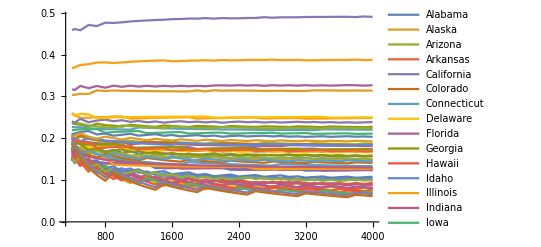

```mathematica
ListPlot[
Transpose[relativeVoterInStateDecisiveProbability],
Joined->True,PlotRange->All
]
```

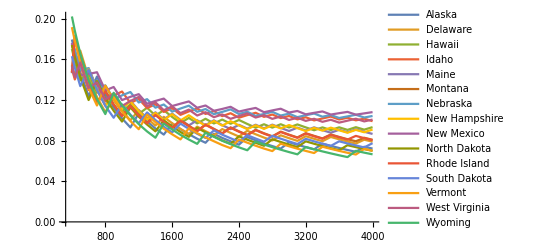

```mathematica
ListPlot[
KeySelect[Transpose[relativeVoterInStateDecisiveProbability],MemberQ[smallest15States,#]&],
Joined->True,PlotRange->All
]
```

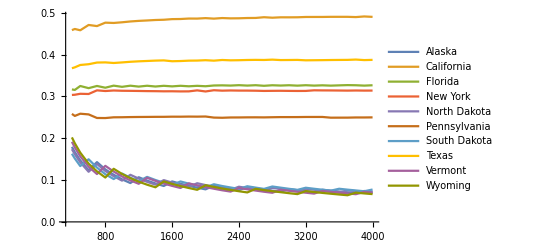

```mathematica
ListPlot[
KeySelect[Transpose[relativeVoterInStateDecisiveProbability],MemberQ[largest5Smallest5States,#]&],
Joined->True,PlotRange->All
]
```

## Historical Data

```mathematica
usaPopulationData1960CSV=FileNameJoin[{NotebookDirectory[],"1960-DATA.csv"}];
usaPopulationData1960=Import[usaPopulationData1960CSV,"Dataset",HeaderLines->1];
```

```mathematica
usaPopulationData1960
```